```mathematica
(*Graphene NN*)
e1={0,1};
e2={Sqrt[3]/2,-1/2};
e3={-Sqrt[3]/2,-1/2};
Plot3D[{Abs[Exp[-I*e1.k]+Exp[-I*e2.k]+Exp[-I*e3.k]]^2/. k->{x,y},-Abs[Exp[-I*e1.k]+Exp[-I*e2.k]+Exp[-I*e3.k]]^2/. k->{x,y}},Element[{x,y},RegularPolygon[4*Pi/(3*Sqrt[3]),6]],BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Plot3D[{Abs[Exp[-I*e1.k]+Exp[-I*e2.k]+Exp[-I*e3.k]]^2/. k->{x,y},-Abs[Exp[-I*e1.k]+Exp[-I*e2.k]+Exp[-I*e3.k]]^2/. k->{x,y}},Element[{x,y},RegularPolygon[6*Pi/(3*Sqrt[3]),6]],BoxRatios->{1,1,1}]
```

```mathematica
(*Haldane NNN *)
```

```mathematica
e1={0,1};
e2={Sqrt[3]/2,-1/2};
e3={-Sqrt[3]/2,-1/2};
v1={Sqrt[3],0};
v2={-Sqrt[3]/2,3/2};
v3={-Sqrt[3]/2,-3/2};
Phi=Pi/6;
t2=1;
t=10;
H[x_,y_]={{-2*t2*(Cos[v1.{x,y}-Phi]+Cos[v2.{x,y}-Phi]+Cos[v3.{x,y}-Phi]),-2*t*(Exp[-I*e1.{x,y}]+Exp[-I*e2.{x,y}]+Exp[-I*e3.{x,y}])},{-2*t*(Exp[I*e1.{x,y}]+Exp[I*e2.{x,y}]+Exp[I*e3.{x,y}]),-2*t2*(Cos[v1.{x,y}+Phi]+Cos[v2.{x,y}+Phi]+Cos[v3.{x,y}+Phi])}};
Plot3D[Sort[Eigenvalues[H[x,y]]],Element[{x,y},RegularPolygon[4*Pi/(3*Sqrt[3]),6]],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Flatten[Table[Table[{Eigenvalues[N[H[x,y]]][[i]],N[x],N[y]},{x,2*Pi/(3*Sqrt[3])-4*Pi/(3*Sqrt[3]*10),2*Pi/(3*Sqrt[3])+4*Pi/(3*Sqrt[3]*10),4*Pi/(3*Sqrt[3]*300)},{y,2*Pi/(3)-4*Pi/(3*10),2*Pi/(3)+4*Pi/(3*10),4*Pi/(3*300)}],{i,1,2}],2]]
```

-Graphics3D-

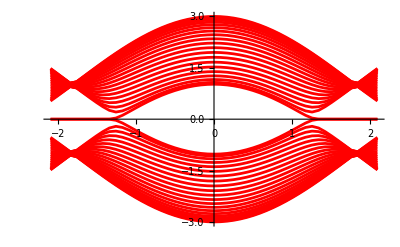

```mathematica
(*half inf*)
n=42;
h[k_]:=Table[If[(Mod[i,2]==0&&j==i+1)||(Mod[j,2]==0&&i==j+1),1,If[(Mod[i,2]==0&&j==i-1)||(Mod[j,2]==0&&i==j-1),2*Cos[Sqrt[3]/2*k],0]],{i,1,n},{j,1,n}];
ListLinePlot[Table[Table[{k,Sort[Eigenvalues[N[h[k]]]][[i]]},{k,-2*Pi/3,2*Pi/3,4*Pi/150}],{i,1,n}],PlotStyle->Red]
```

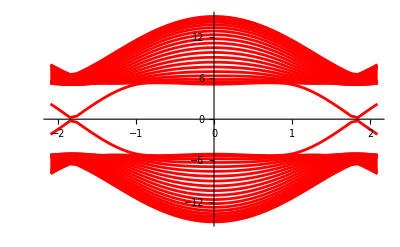

```mathematica
(*NNN jackiw-rebbi*)
n=42;
t=5;
t'=1;
Phi=Pi/2;
h[n_,k_,Phi_,t_,t2_]:=Table[If[i==j,2*t2*Cos[Sqrt[3]*k+((-1)^i)*Phi],If[Abs[i-j]==2,2*t2*Cos[Sqrt[3]/2*k-((-1)^i)*Phi],If[(j==i+1&&Mod[j,2]==0)||(i==j+1&&Mod[i,2]==0),2*t*Cos[Sqrt[3]/2*k],If[(j==i+1&&Mod[i,2]==0)||(i==j+1&&Mod[j,2]==0),t,0]]]],{i,1,n},{j,1,n}];
ListLinePlot[Table[Table[{k,Sort[Eigenvalues[N[h[n,k,Phi,t,t']]]][[i]]},{k,-2*Pi/3,2*Pi/3,4*Pi/150}],{i,1,n}],PlotStyle->Red]
```